```mathematica
<<ThinLayer`
```

```mathematica
tlSetLayer[1,{22.56,12.38,17.35,3.15,2.38}];
tlSetLayer[2,{26.73,12.51,26.73,7.11,2.22}];
tlSetLayer[3,{11.25,6.066,11.25,2.592,1.8}];
tlSetLayer[4,{11.25+I,6.066,26.25,2.592,1.8}];
tlSetLayer[5,{11.25+I,2.066,19.25,2.592,1.8}];
tlSetLayer[6,{11.25+I,6.066,23.25,2.592,1.8}];
tlSetLayer[7,{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->2.0002/.vs->1.0002/.den->2.0002];
tlSetLayer[8,{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->3.0002/.vs->1.5002/.den->3.0002];

tlSetLayer[9,{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->4.500/.vs->2.500/.den->2.750];

tlSetLayer[10,{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den}/.vp->2.920/.vs->1.400/.den->2.180];
```

```mathematica
Module[
{ωList,Noffsets,scaling,layers,thicknesses,kList,ϕ,ref,dHT,zs,zr,calclist,pmin,overburden,model,c11,ρ,phorlayer1,k,FindMaxK,K,dList,Nfreq,maxfreq,deltafreq,kMax,rMax,J,Su,Sd,U,f2,p,pMax,Σ1,Σ2,B,S1,S2,b,u,σ,HTvec,integrand},

zs=.3;
zr=.4;

(*layers={1,2,3,2};
overburden=3;
model={overburden,Sequence@@layers,overburden};*)

layers={8};
overburden=7;
model={overburden,Sequence@@layers};
dList={0,0};

{c11,ρ}=tlGetStiffness[overburden][[{1,-1}]];
phorlayer1=(c11/ρ)^(-1/2) ;


(*

(*==== MULLER ====*)

U[ω_,k_]:=Reverse@DiagonalMatrix[tlQLmatrices[overburden,k/ω][[1]]]+DiagonalMatrix[{k/ω,-k/ω}];
J[k_,r_]:=DiagonalMatrix[{BesselJ[1,k r],BesselJ[0,k r]}];
Su[ω_,k_]:={-k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
Sd[ω_,k_]:={k/ω,(k/ω)^2/tlQLmatrices[overburden,k/ω][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,k/ω][[1]]];
ref[ω_,k_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]].tlReflectivity[model,dList,k/ω,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,k/ω][[1]] zr]])//Chop;
integrand[ω_,k_]:={{-1,0},{0,ⅈ}}.U[ω,k].(Su[ω,k]+ref[ω,k].Sd[ω,k]);*)

(*U[p_]:=(*Reverse@DiagonalMatrix[tlQLmatrices[overburden,p][[1]]]+*)DiagonalMatrix[{p,-p}];
J[p_,ω_,r_]:=DiagonalMatrix[{N@BesselJ[1,p ω r],N@BesselJ[0,p ω r]}];
Su[p_,ω_]:={-1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
Sd[p_,ω_]:={1,p/tlQLmatrices[overburden,p][[1,2]]}Exp[-ⅈ ω zs tlQLmatrices[overburden,p][[1]]];
ref[p_,ω_]:=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω]ᵀ.DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//Chop;
(*f2[p_,ω_]:=ω({{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])/4./Pi/ρ//Chop;*)
f2[p_,ω_,r_]:=p(J[p,ω,r]{{-1,0},{0,ⅈ}}).U[p].(Su[p,ω]+ref[p,ω].Sd[p,ω])//Chop;
*)
(*
ref[p_,ω_]=(DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]].tlReflectivity[model,dList,p,ω].DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zr]])//N;

(*==== URSIN ====
stress-displacement as in Stovas and Ursin:
b = [ω Uz, -Sr, Sz, ωUr] ;
Tranformed back to space-time:
b = [uz, σrz, σzz, ur] ;

*)

Σ1[p_,ω_]=1/(√2)tlQLmatrices[overburden,p][[2]]ᵀ.{-1/(ρ ω) ,0};(*σzz force*)
Σ2[p_,ω_]=Σ1[p,ω];
S1[p_,ω_]=DiagonalMatrix[Exp[I ω tlQLmatrices[overburden,p][[1]] zs]].Σ1[p,ω];
S2[p_,ω_]=DiagonalMatrix[Exp[-I ω tlQLmatrices[overburden,p][[1]] zs]].Σ2[p,ω];
U[p_,ω_]=ref[p,ω].S2[p,ω]-S1[p,ω];
B[p_,ω_]={Sequence@@((I tlQLmatrices[overburden,p][[2]])/(√2).U[p,ω]),Sequence@@((tlQLmatrices[overburden,p][[3]])/(√2).U[p,ω])};
b[p_,ω_,r_]=p ω^2 B[p,ω]{1/ω,-1,1,1/ω}{BesselJ[0,p ω r],BesselJ[1,p ω r],BesselJ[0,p ω r],BesselJ[1,p ω r]};

(*{ur,uz}*)
u[p_,ω_,r_]=b[p,ω,r][[{4,1}]];
(*{σrz,σzz}*)
σ[p_,ω_,r_]=b[p,ω,r][[{2,3}]];
*)
(*FindMaxK[ω_,tol_]:=Module[{kmax,phase},
kmax=phorlayer1 ω;
phase[k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zr)].DiagonalMatrix[E^(I ω tlQLmatrices[overburden,k/ω][[1]] zs)])[[1,1]];
FindMinimum[{Abs[phase[k]],k>0},{k,kmax},AccuracyGoal->tol][[2,1,2]]
];*)

HTvec[p_,ω_,r_]=p{BesselJ[0,p ω r],BesselJ[1,p ω r],BesselJ[0,p ω r],BesselJ[1,p ω r]};
integrand[p_,ω_,r_]=HTvec[p,ω,r] tlResponse[model,dList,p,ω,zs,zr];

Nfreq=100;
Noffsets=500;

maxfreq=50;
deltafreq=maxfreq/Nfreq;
ωList=2Pi Range[deltafreq,maxfreq,deltafreq]//N;

(*pMax=10;

AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,tlResponse[model,dList,#,ωList[[i]],zs,zr][[1]]&,0,pMax],
{i,1,Length@ωList}];
freqvec=ωList;
]*)

(*With[{p0=.1,ω=2Pi 20,r=.3},
tlResponse[model,dList,p0,ω,zs,zr]
]*)

Module[

{Np=5000,pmax=4,pList,dp,r=.3},
dp=pmax/Np;
pList=Range[0,pmax,dp];

DistributeDefinitions[pList,ωList,dp,integrand];

freqvec=ωList;

integrand[.1,2Pi 1,r]

(*testZ=
ParallelTable[
dp Total[integrand[#,ω,r][[1]]&/@pList],
{ω,ωList},DistributedContexts->{"ThinLayer`Private`"}];*)


];


(*AbsoluteTiming[
testZ=
Table[
tlDHT2[Noffsets,ref[#,ωList[[i]]][[1,1]]&,0,pMax],
{i,1,Length@ωList}];


freqvec=ωList;
]*)


(*Table[
Module[{ω0=ωList[[i]],testk},
{testk=FindMaxK[ω0,11],ListLinePlot[Transpose[ReIm@ref[ω0,#]&/@Range[.5testk,1.5testk,testk/100]],ImageSize->600,PlotRange->Full]}
]
,{i,Length@ωList}]
*)


(*With[{ω=2Pi 300, tol=10},
K=FindMaxK[ω,tol];
{ref[ω,#]&/@Range[0,K,K/(Noffsets-1)],K}
]*)


(*With[{ω=2.Pi 150},
{ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,kMax][[;;,2]])ᵀ,PlotLabel->kMax,ImageSize->Large,PlotRange->Full],
ListLinePlot[(ReIm@tlDHT2[Noffsets,ref[ω,#]&,0,FindMaxK[ω,11]][[;;,2]])ᵀ,PlotLabel->FindMaxK[ω,11],ImageSize->Large,PlotRange->Full]}
]*)







(*rMax=3;
pMax=8;

AbsoluteTiming[
testR=
Table[
tlDHT2[Noffsets,f2[#,ωList[[i]]][[1]]&,1,pMax],
{i,1,Length@ωList}];

testZ=
Table[
tlDHT2[Noffsets,f2[#,ωList[[i]]][[2]]&,0,pMax],
{i,1,Length@ωList}];

freqvec=ωList;
]*)


]
```

Maximum offset = 209.597

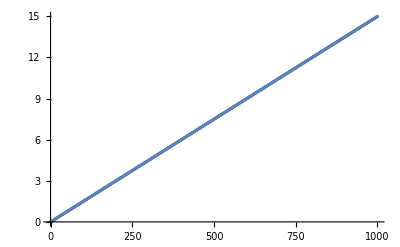

```mathematica
With[{Np=1000,pmax=15,p=0},
Print["Maximum offset = "<>ToString[BesselJZero[p,Np+1]/pmax//N]];
ListPlot[(pmax Table[N[BesselJZero[p,n]],{n,1,Np}])/BesselJZero[p,Np+1]]
]
```

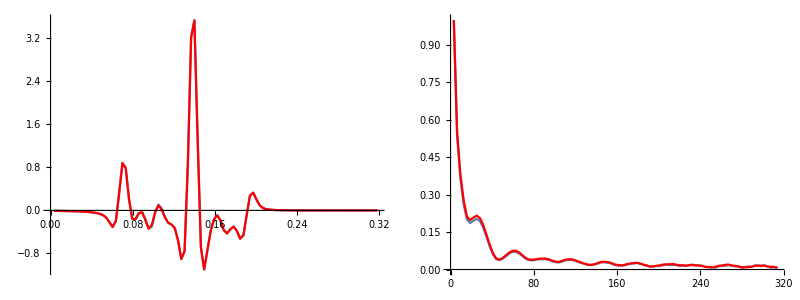

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=testZ,int,regoffsets,regRefl,reflSource,fRicker=15,reflTX,t,reflSourceIvan,importIvan,ivanUz,ivanω,reflTXIvan},

u=u;
reflSource=u(rickerSpectrum[#,2Pi fRicker]&/@freqvec);
reflSource=reflSource/Max[Abs@reflSource];

reflTX=
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource)~Join~{0+0. I}~Join~reflSource,Length@freqvec]][[1;;Length@freqvec]];
t=Range[Length[freqvec]]/((freqvec[[2]]-freqvec[[1]]) Length[freqvec]);


importIvan=Quiet@Import[NotebookDirectory[]<>"..\..\ivan.txt","Data"];
{ivanω,ivanUz}=Transpose[{#[[1]],#[[2]]+I#[[3]]}&/@importIvan];

reflSourceIvan= ivanUz(rickerSpectrum[#,2Pi fRicker]&/@ivanω);
reflSourceIvan=reflSourceIvan/Max[Abs@reflSourceIvan];
reflTXIvan=
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSourceIvan)~Join~{0+0. I}~Join~reflSourceIvan,Length@ivanω]][[1;;Length@ivanω]];


(*ListLinePlot[{t,Re@reflTXIvan}ᵀ,PlotRange->Full,PlotStyle->Red]*)
{{Show[ListLinePlot[{t,Re@reflTX}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{t,Re@reflTXIvan}ᵀ,PlotRange->Full,PlotStyle->Red]],
Show[ListLinePlot[{freqvec,(Abs@u)/(Max@Abs@u)}ᵀ,PlotRange->Full,ImageSize->Large],ListLinePlot[{ivanω,(Abs@ivanUz)/(Max@Abs@ivanUz)}ᵀ,PlotRange->Full,PlotStyle->Red]]}}//TableForm
(*ListLinePlot[{{ivanω,Im@ivanUz}ᵀ,{freqvec,Im@u}ᵀ},PlotRange->Full]*)

]
```

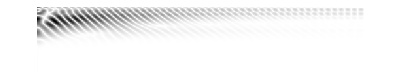

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];

Module[{u=testZ,maxX,minX,int,regoffsets,regRefl,reflSource,fRicker=5,reflTX},
{maxX,minX}={Min@Re@u[[;;,-1,1]],Max@Re@u[[;;,1,1]]};

int=Table[Interpolation[Chop@u[[i,;;,;;]]],{i,1,Dimensions[u][[1]]}];
regoffsets=Range[minX,maxX,(maxX-minX)/(Dimensions[u][[2]]-1)]//N;
regRefl=Table[int[[i]][#]&/@regoffsets,{i,1,Dimensions[u][[1]]}];
regRefl=u[[;;,;;,2]];

reflSource=regRefl(rickerSpectrum[#,2Pi fRicker]&/@freqvec);

reflTX=Table[
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource[[;;,i]])~Join~{0+0. I}~Join~reflSource[[;;,i]],Length@freqvec]][[1;;Length@freqvec]]
,{i,1,Dimensions[reflSource][[2]]}];

testTX=reflTX;
offsets=u[[;;,;;,1]]//Chop;
ArrayPlot[(reflTX)ᵀ]


]
```

```mathematica
Manipulate[ListLinePlot[Abs@testZ[[;;,i,2]],PlotRange->Full],{i,1,Dimensions[testZ][[2]],1}]
```

```mathematica
{maxX,minX}={Min@Re@test[[;;,-1,1]],Max@Re@test[[;;,1,1]]}
```

{200.,0.496287}

```mathematica
int=Table[Interpolation[Chop@test[[i,;;,;;]]],{i,1,Dimensions[test][[1]]}];
```

```mathematica
regoffsets=Range[minX,maxX,(maxX-minX)/(Dimensions[test[[1]]][[1]])]//N;
```

```mathematica
regRefl=Table[int[[i]][#]&/@regoffsets,{i,1,Dimensions[test][[1]]}];
regRefl=test[[;;,;;,2]];
```

```mathematica
rickerSpectrum[w_,wp_]:=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];
```

```mathematica
reflSource=PadLeft[regRefl,Dimensions[regRefl]+{1,0}](rickerSpectrum[#,2Pi 10]&/@({0}~Join~freqvec));
```

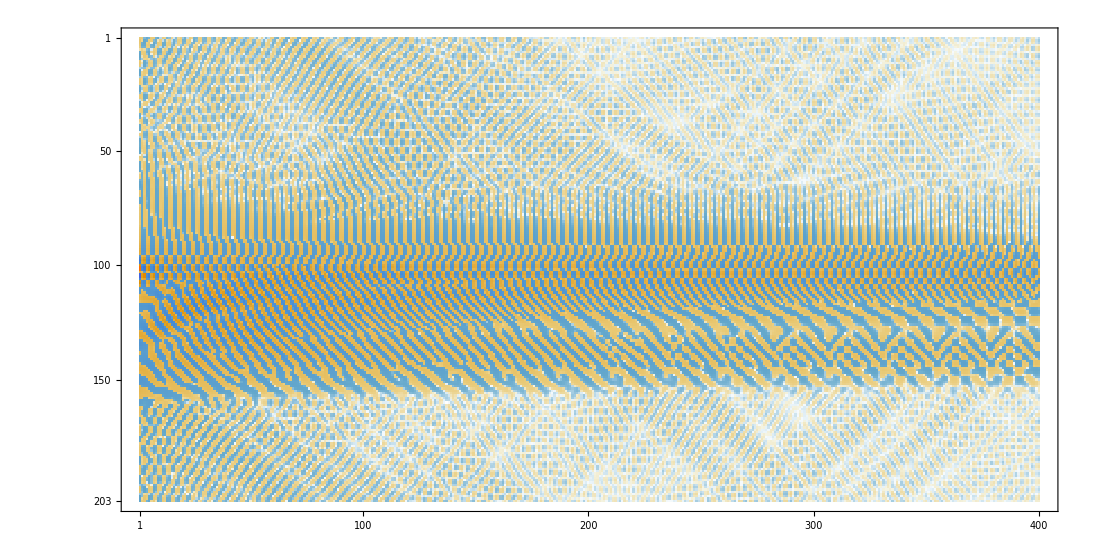

```mathematica
reflTX=Table[RotateRight[
InverseFourier[RotateLeft[(Reverse@Conjugate@reflSource[[;;,i]])~Join~{0+0. I}~Join~reflSource[[;;,i]],Length@freqvec+1]]
,Length@freqvec]
,{i,1,Dimensions[reflSource][[2]]}]//Chop;

MatrixPlot[(reflTXᵀ)]
```

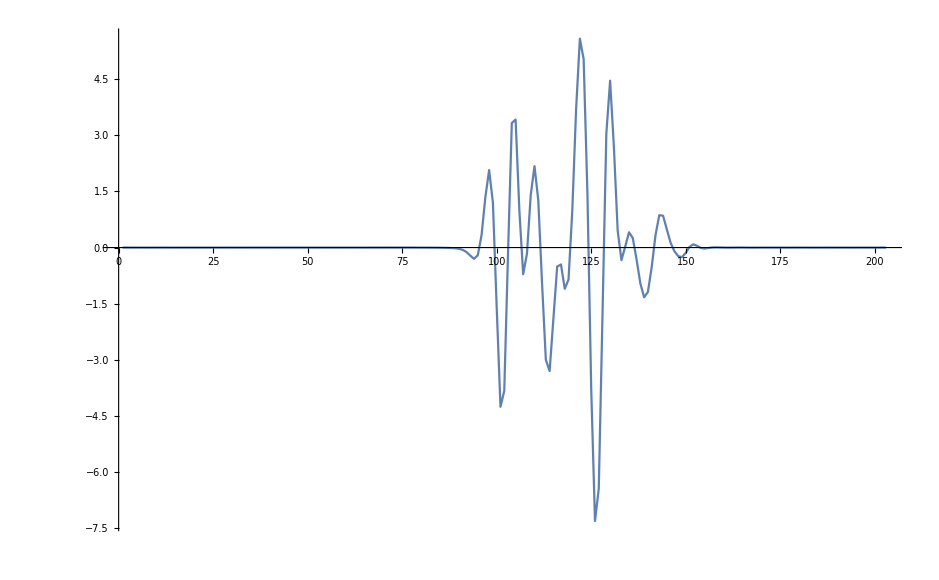

```mathematica
ListLinePlot[reflTX[[10,;;]],PlotRange->Full]
```

```mathematica
fset=Module[{resamp,tSamp=1024,sampRate=1/512,maxω,δω,offSamp=400},
resamp=ArrayResample[test2,{tSamp,offSamp}];
maxω=1024;
δω=maxω/tSamp;
Table[RotateRight[InverseFourier[RotateLeft[tSamp rickerSpectrum[Range[-N@maxω,N@maxω,δω],2 π 30] (Reverse@Conjugate@resamp[[;;,i,2]])~Join~{1.+0. I}~Join~resamp[[;;,i,2]],tSamp],FourierParameters->{1,-1}],tSamp],{i,1,offSamp}]];
```

```mathematica
Module[{ωList,noffsets,scaling,layers,thicknesses,kList,ϕ,ref,dHT,zs,zr,calclist},zs=.5;zr=.6;
layers={1,2,3,2};
thicknesses={.02,.5,.2,.08};
ωList=Range[1.,1024.,8.];
noffsets=128;
scaling=35.;
kList=scaling Range[0,π,π/(noffsets-1)];
ref[ω_,k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zs)].tlReflectivity[{3,Sequence@@layers,3},{1,Sequence@@thicknesses,1},k/ω,ω].DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zr)])[[1,1]];
ref[ω_,k_?VectorQ]:=ref[ω,#]&/@k;
dHT=tlDiscreteHankelTransform[#1,0.,#2]&;
AbsoluteTiming[test128=ref[#,kList]&/@ωList;
test2128=tlDiscreteHankelTransform[#,0.,scaling π]&/@test128;]]
```

{74.6581,Null}

```mathematica
Module[{ωList,noffsets,scaling,layers,thicknesses,kList,ϕ,ref,dHT,zs,zr,calclist},zs=.5;zr=.6;
layers={1,2,3,2};
thicknesses={.02,.5,.2,.08};
ωList=Range[1.,1024.,8.];
noffsets=512;
scaling=35.;
kList=scaling Range[0,π,π/(noffsets-1)];
ref[ω_,k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zs)].tlReflectivity[{3,Sequence@@layers,3},{1,Sequence@@thicknesses,1},k/ω,ω].DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zr)])[[1,1]];
ref[ω_,k_?VectorQ]:=ref[ω,#]&/@k;
dHT=tlDiscreteHankelTransform[#1,0.,#2]&;
AbsoluteTiming[test512=ref[#,kList]&/@ωList;
test2512=tlDiscreteHankelTransform[#,0.,scaling π]&/@test512;]]
```

{418.461,Null}

```mathematica
Module[{ωList,noffsets,scaling,layers,thicknesses,kList,ϕ,ref,dHT,zs,zr,calclist},zs=.5;zr=.6;
layers={1,2,3,2};
thicknesses={.02,.5,.2,.08};
ωList=Range[1.,1024.,8.];
noffsets=1024;
scaling=35.;
kList=scaling Range[0,π,π/(noffsets-1)];
ref[ω_,k_]:=(DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zs)].tlReflectivity[{3,Sequence@@layers,3},{1,Sequence@@thicknesses,1},k/ω,ω].DiagonalMatrix[E^(I ω tlQLmatrices[1,k/ω][[1]] zr)])[[1,1]];
ref[ω_,k_?VectorQ]:=ref[ω,#]&/@k;
dHT=tlDiscreteHankelTransform[#1,0.,#2]&;
AbsoluteTiming[test1024=ref[#,kList]&/@ωList;
test21024=tlDiscreteHankelTransform[#,0.,scaling π]&/@test1024;]]
```

{1079.9,Null}

```mathematica
rickerSpectrum[w_,wp_]=(2 w^2)/(Sqrt[π] wp^3) Exp[-(w^2/wp^2)];
```

```mathematica
fset=Module[{resamp,tSamp=1024,sampRate=1/512,maxω,δω,offSamp=400},resamp=ArrayResample[test2,{tSamp,offSamp}];
maxω=1024;
δω=maxω/tSamp;
Table[RotateRight[InverseFourier[RotateLeft[tSamp rickerSpectrum[Range[-N@maxω,N@maxω,δω],2 π 30] (Reverse@Conjugate@resamp[[;;,i,2]])~Join~{1.+0. I}~Join~resamp[[;;,i,2]],tSamp],FourierParameters->{1,-1}],tSamp],{i,1,offSamp}]];
```

```mathematica
test2512[[1,All,1]]//Chop
```

{0.00348085,0.00799001,0.0125258,0.0170676,0.0216117,0.0261569,0.0307027,0.0352489,0.0397953,0.0443419,0.0488887,0.0534355,0.0579824,0.0625293,0.0670763,0.0716234,0.0761704,0.0807175,0.0852646,0.0898118,0.0943589,0.0989061,0.103453,0.108,0.112548,0.117095,0.121642,0.126189,0.130736,0.135284,0.139831,0.144378,0.148925,0.153473,0.15802,0.162567,0.167114,0.171661,0.176209,0.180756,0.185303,0.18985,0.194398,0.198945,0.203492,0.20804,0.212587,0.217134,0.221681,0.226229,0.230776,0.235323,0.23987,0.244418,0.248965,0.253512,0.258059,0.262607,0.267154,0.271701,0.276248,0.280796,0.285343,0.28989,0.294438,0.298985,0.303532,0.308079,0.312627,0.317174,0.321721,0.326268,0.330816,0.335363,0.33991,0.344458,0.349005,0.353552,0.358099,0.362647,0.367194,0.371741,0.376288,0.380836,0.385383,0.38993,0.394478,0.399025,0.403572,0.408119,0.412667,0.417214,0.421761,0.426308,0.430856,0.435403,0.43995,0.444498,0.449045,0.453592,0.458139,0.462687,0.467234,0.471781,0.476329,0.480876,0.485423,0.48997,0.494518,0.499065,0.503612,0.50816,0.512707,0.517254,0.521801,0.526349,0.530896,0.535443,0.53999,0.544538,0.549085,0.553632,0.55818,0.562727,0.567274,0.571821,0.576369,0.580916,0.585463,0.590011,0.594558,0.599105,0.603652,0.6082,0.612747,0.617294,0.621842,0.626389,0.630936,0.635483,0.640031,0.644578,0.649125,0.653672,0.65822,0.662767,0.667314,0.671862,0.676409,0.680956,0.685503,0.690051,0.694598,0.699145,0.703693,0.70824,0.712787,0.717334,0.721882,0.726429,0.730976,0.735524,0.740071,0.744618,0.749165,0.753713,0.75826,0.762807,0.767355,0.771902,0.776449,0.780996,0.785544,0.790091,0.794638,0.799186,0.803733,0.80828,0.812827,0.817375,0.821922,0.826469,0.831016,0.835564,0.840111,0.844658,0.849206,0.853753,0.8583,0.862847,0.867395,0.871942,0.876489,0.881037,0.885584,0.890131,0.894678,0.899226,0.903773,0.90832,0.912868,0.917415,0.921962,0.926509,0.931057,0.935604,0.940151,0.944699,0.949246,0.953793,0.95834,0.962888,0.967435,0.971982,0.97653,0.981077,0.985624,0.990171,0.994719,0.999266,1.00381,1.00836,1.01291,1.01746,1.022,1.02655,1.0311,1.03564,1.04019,1.04474,1.04929,1.05383,1.05838,1.06293,1.06748,1.07202,1.07657,1.08112,1.08566,1.09021,1.09476,1.09931,1.10385,1.1084,1.11295,1.1175,1.12204,1.12659,1.13114,1.13568,1.14023,1.14478,1.14933,1.15387,1.15842,1.16297,1.16752,1.17206,1.17661,1.18116,1.1857,1.19025,1.1948,1.19935,1.20389,1.20844,1.21299,1.21754,1.22208,1.22663,1.23118,1.23572,1.24027,1.24482,1.24937,1.25391,1.25846,1.26301,1.26756,1.2721,1.27665,1.2812,1.28574,1.29029,1.29484,1.29939,1.30393,1.30848,1.31303,1.31758,1.32212,1.32667,1.33122,1.33576,1.34031,1.34486,1.34941,1.35395,1.3585,1.36305,1.3676,1.37214,1.37669,1.38124,1.38579,1.39033,1.39488,1.39943,1.40397,1.40852,1.41307,1.41762,1.42216,1.42671,1.43126,1.43581,1.44035,1.4449,1.44945,1.45399,1.45854,1.46309,1.46764,1.47218,1.47673,1.48128,1.48583,1.49037,1.49492,1.49947,1.50401,1.50856,1.51311,1.51766,1.5222,1.52675,1.5313,1.53585,1.54039,1.54494,1.54949,1.55403,1.55858,1.56313,1.56768,1.57222,1.57677,1.58132,1.58587,1.59041,1.59496,1.59951,1.60405,1.6086,1.61315,1.6177,1.62224,1.62679,1.63134,1.63589,1.64043,1.64498,1.64953,1.65407,1.65862,1.66317,1.66772,1.67226,1.67681,1.68136,1.68591,1.69045,1.695,1.69955,1.70409,1.70864,1.71319,1.71774,1.72228,1.72683,1.73138,1.73593,1.74047,1.74502,1.74957,1.75411,1.75866,1.76321,1.76776,1.7723,1.77685,1.7814,1.78595,1.79049,1.79504,1.79959,1.80414,1.80868,1.81323,1.81778,1.82232,1.82687,1.83142,1.83597,1.84051,1.84506,1.84961,1.85416,1.8587,1.86325,1.8678,1.87234,1.87689,1.88144,1.88599,1.89053,1.89508,1.89963,1.90418,1.90872,1.91327,1.91782,1.92236,1.92691,1.93146,1.93601,1.94055,1.9451,1.94965,1.9542,1.95874,1.96329,1.96784,1.97238,1.97693,1.98148,1.98603,1.99057,1.99512,1.99967,2.00422,2.00876,2.01331,2.01786,2.0224,2.02695,2.0315,2.03605,2.04059,2.04514,2.04969,2.05424,2.05878,2.06333,2.06788,2.07242,2.07697,2.08152,2.08607,2.09061,2.09516,2.09971,2.10426,2.1088,2.11335,2.1179,2.12244,2.12699,2.13154,2.13609,2.14063,2.14518,2.14973,2.15428,2.15882,2.16337,2.16792,2.17247,2.17701,2.18156,2.18611,2.19065,2.1952,2.19975,2.2043,2.20884,2.21339,2.21794,2.22249,2.22703,2.23158,2.23613,2.24067,2.24522,2.24977,2.25432,2.25886,2.26341,2.26796,2.27251,2.27705,2.2816,2.28615,2.29069,2.29524,2.29979,2.30434,2.30888,2.31343,2.31798,2.32253,2.32707}

```mathematica
test2128
test2512
test21024
```

```mathematica
ft=InverseFourier[#1[[;;,#2,2]]]&
```

InverseFourier[#1⟦1;;All,#2,2⟧]&

```mathematica
ArrayPlot[(fset)[[;;,500;;1300]]//Chop//Transpose//Reverse]
```

-Graphics-

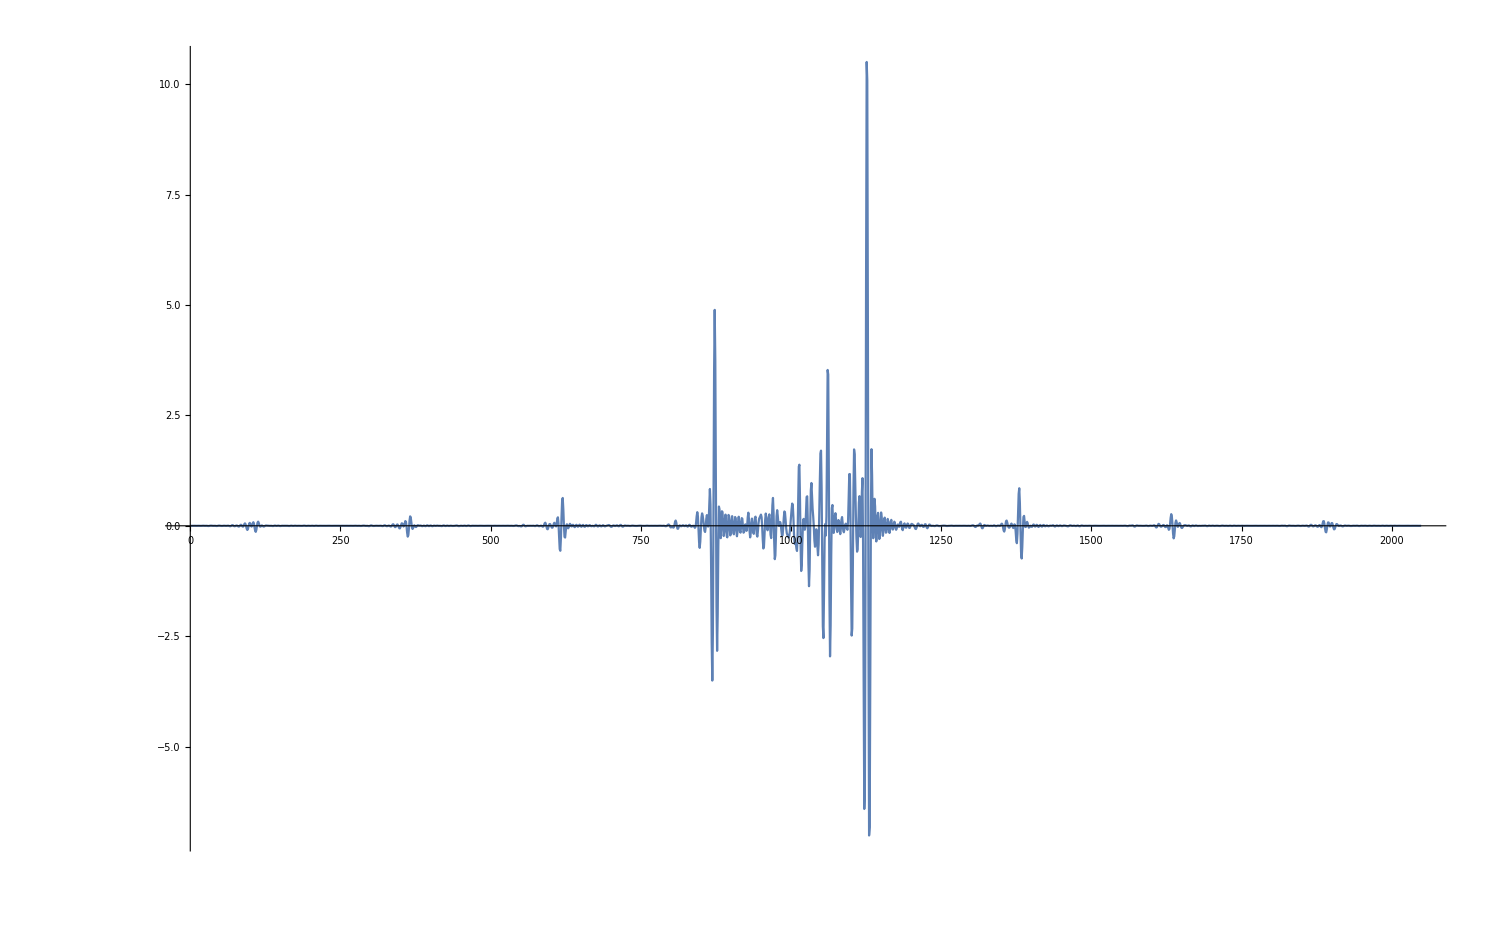

```mathematica
ListLinePlot[Chop@fset[[100,;;]],PlotRange->Full]
```

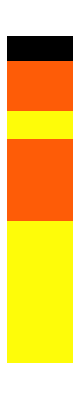

```mathematica
tlVisualiseModel[{3,1,2,3,2,3}//Reverse,{1,.02,.05,.02,.08,.1}//Reverse,1]
```